# Blending Model Project

This notebook will help you with your implementation of the final project. It provides the function definitions for you to fill out as well as tests to verify that you’ve written each piece.

Since this project is bigger than any we’ve done before, it will be easier to work with smaller more modular pieces of code that we can verify independently. As such, we’ve included tests in the starter code below to help you verify that you’re on the right track. You don’t need to use this starter code to solve the project, and if you feel confident that you can do it by yourself, by all means, have at it! Otherwise, we welcome you to follow along with a little bit of hand holding from us.

## Constants

We will be drawing our creatures in a 50x50 area. Let’s define some constants so that we don’t have to write the number 50 everywhere.

```mathematica
xmin=0;xmax=50;
ymin=0;ymax=50;
```

## Creatures

We will represent our creatures as expressions with the head BlendingCreature. Let’s create a few prototypical creatures that we will make use of in our tests:

```mathematica
bc1=BlendingCreature[0.1,{20,40}];
bc2=BlendingCreature[0.4,{30,40}];
bc3=BlendingCreature[0.7,{40,30}];
bc4=BlendingCreature[0.9,{40,20}];
```

The first part of our creature is its Trait value. The second part is the location (x, y coordinate) of the creature.

## Accessors

The first function to write is the Traits function. This function will get the traits of our BlendingCreature. So for example, Traits[bc1] should return 0.1.

```mathematica
Traits[creature_BlendingCreature]:=Null(* Fill me in *)
```

Our second function gets the location of the creature.

```mathematica
Location[creature_BlendingCreature]:=Null(* Fill me in *)
```

### Tests

#### Verify the accessors

Here’s our first set of tests. These should evaluate the True if you’ve written your code above correctly!

```mathematica
Traits[bc1]===0.1
```

```mathematica
Traits[bc2]===0.4
```

```mathematica
Location[bc3]==={40,30}
```

```mathematica
Location[bc4]==={40,20}
```

## Evolution

Now let’s write the functions that will evolve our creatures.

The first function is Procreate. Procreate will evolve two blending creatures by blending their traits and producing some number of offspring.

Use the mean of the parent creatures’ traits as the offspring’s traits.

Use a random number between xmin, ymin and xmax, ymax for the offspring's location.

```mathematica
Procreate[mother_BlendingCreature,father_BlendingCreature,OptionsPattern[{ChildCount->1}]]:=Null(* Fill me in *)
```

### Tests

#### Verify that Procreate of bc1 and bc2 produces offspring with trait value 0.25

```mathematica
MatchQ[Procreate[bc1,bc2],{BlendingCreature[0.25,{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

#### Verify that Procreate with ChildCount → 2 produces two offspring

```mathematica
MatchQ[Procreate[bc1,bc2,ChildCount->2],offspring:{BlendingCreature[0.25,_]..}/;Length[offspring]==2]
```

## Initialization

Create a function to generate a population of blending creatures, where size is the number of creatures in the initial generation.

```mathematica
InitializeBlendingPopulation[size_Integer]:=Null(* Fill me in *)
```

### Tests

#### Verify that InitializeBlendingPopulation returns 20 creatures

```mathematica
MatchQ[InitializeBlendingPopulation[20],creatures:{_BlendingCreature..}/;Length[creatures]==20]
```

## Simulation

Now we need a function that will evolve one generation into the next generation. The evolve function must be stable, meaning that the number of creatures in the next generation must be equal to the number in the previous generation. Code the Evolve function to pick pairs of parent creatures, and have them produce pairs of offspring. Then return the flattened list of offspring as the next generation.

```mathematica
Evolve[population:{__BlendingCreature}]:=Null(* Fill me in *)
```

Evolve generates the next generation from the current generation. We need a function to simulate all the generations in our simulation. We will call this function BlendingSimulate. We’ve written some starter code for you. BlockRandom is a function that localizes pseudorandom number generation. SeedRandom is a function that sets the current random number seed. Long story short, these functions allow our simulation to be repeatable for the same seed values.

```mathematica
BlendingSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
Null(* Fill me in *)
]
```

Extra credit: how would you modify BlendingSimulate so that it doesn’t recompute the simulation every time the function is called with the same arguments?

### Tests

#### Verify that Evolving a population produces a new population of the same size

```mathematica
With[{initPop=InitializeBlendingPopulation[20]},
With[{nextGen=Evolve[initPop]},
And[
MatchQ[nextGen,creatures:{_BlendingCreature..}/;Length[creatures]==20],
nextGen=!=initPop
]
]]
```

#### Verify that the simulation is repeatable for the same arguments

```mathematica
BlendingSimulate[0,20,200]===BlendingSimulate[0,20,200]
```

#### Verify that the simulation produces different results for different seeds

```mathematica
BlendingSimulate[0,20,200]=!=BlendingSimulate[1,20,200]
```

## Rendering

The ColorBinarize function is provided to help you render readable text on your creatures.

```mathematica
ColorBinarize[color_RGBColor]:=Round[Mean[List@@color]]/.{0->White,1->Black}
```

HeredityColor returns the color to use to render the creature. If the trait is 0, render the creature as black. If the trait is 1, render the creature as white. For all other values between 0 and 1, render the creature using a grayscale gradient.

```mathematica
HeredityColor[creature_BlendingCreature]:=Null(* Fill me in *)
```

CreatureName returns the string that will go inside each creature’s disk. It shouldn’t be long, so for our blending trait, round it to the nearest tenth.

```mathematica
CreatureName[creature_BlendingCreature]:=Null(* Fill me in *)
```

Our first render function will return the drawing commands to render the creature as a disk, with background color HeredityColor, and its name in the center.

```mathematica
Render[creature_BlendingCreature]:=Null(* Fill me in *)
```

Our second render function will return the drawing commands to render a population of creatures.

```mathematica
Render[population:{___BlendingCreature}]:=Null(* Fill me in *)
```

Our last render function produces the histogram of the various trait values for a given population.

```mathematica
TraitHistogram[population:{___BlendingCreature}]:=Null(* Fill me in *)
```

### Tests

#### Verify that HeredityColor of bc1 is GrayLevel of 0.1

```mathematica
ColorConvert[HeredityColor[bc1],"RGB"]===RGBColor[0.1,0.1,0.1]
```

#### Verify that HeredityColor of bc2 is GrayLevel of 0.4

```mathematica
ColorConvert[HeredityColor[bc2],"RGB"]===RGBColor[0.4,0.4,0.4]
```

#### Verify that rendering a creature returns a list

```mathematica
MatchQ[Render[bc1],_List]
```

#### Verify that rendering a population returns a list

```mathematica
MatchQ[Render[InitializeBlendingPopulation[20]],_List]
```

#### Verify that we can render a column of graphics

This is not an automated test. Eyeball your render and make sure it looks like our render:

```mathematica
Column[{
TraitHistogram[BlendingSimulate[0,20,200][[2]]],
Graphics[Render[BlendingSimulate[0,20,200][[2]]],ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}},ImagePadding->20]
}, Center]
```

Which should look something like:

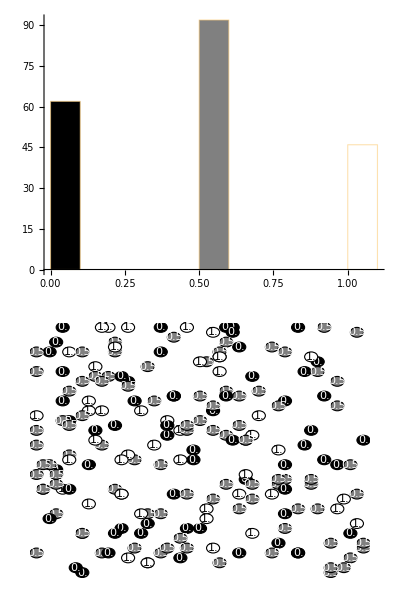

## Manipulate

Your Manipulate should be able to control the seed value and the currently visible generation!